```mathematica
ClearAll[xiTwelve,rootsTwelve,rootsTwelveConj];
ClearAll[conjL12,toComplexConj,toComplex];
```

```mathematica
xiTwelve[k_]:={Cos[2*Pi*k/12],Sin[2*Pi*k/12]};
```

```mathematica
rootsTwelve=Map[xiTwelve,Range[0,12]];
```

```mathematica
(* that's how we get k=4 *)
xiTwelve[4]+xiTwelve[0]-xiTwelve[2]
```

{0,0}

```mathematica
(* that's how we get k=5 *)
xiTwelve[5]+xiTwelve[1]-xiTwelve[3]
```

{0,0}

```mathematica
rootsTwelveConj=Map[xiTwelve[-#]&,Range[0,12]];
```

```mathematica
conjL12[{x0_,x1_,x2_,x3_}]:={x0+x2,x1,-x2,-x1-x3};
toComplexConj[{x0_,x1_,x2_,x3_}]:=x0*Part[rootsTwelveConj,1]+x1*Part[rootsTwelveConj,2]+x2*Part[rootsTwelveConj,3]+x3*Part[rootsTwelveConj,4];
toComplex[{x0_,x1_,x2_,x3_}]:=x0*Part[rootsTwelve,1]+x1*Part[rootsTwelve,2]+x2*Part[rootsTwelve,3]+x3*Part[rootsTwelve,4];
```

```mathematica
toComplex[{a0,a1,a2,a3}]
```

{a0+(√3 a1)/2+a2/2,a1/2+(√3 a2)/2+a3}

```mathematica
toComplexConj[{a0,a1,a2,a3}]
```

{a0+(√3 a1)/2+a2/2,-a1/2-(√3 a2)/2-a3}

```mathematica
toComplex[conjL12[{a0,a1,a2,a3}]]-toComplexConj[{a0,a1,a2,a3}]
```

{0,0}

```mathematica
conjL12[conjL12[{a0,a1,a2,a3}]]
```

{a0,a1,a2,a3}

```mathematica
SetDirectory["/homes/tjakobi/PhD_Work/radialprojection"];
```

```mathematica
mylist0=RunThrough["./cyclotomic_radial",Null];
Length[Part[mylist0,1]]
```

2298

```mathematica
edgeIndices0=Part[mylist0,2];
Length[edgeIndices0]
```

5106

```mathematica
verts0=Map[toComplex,Part[mylist0,1]];
```

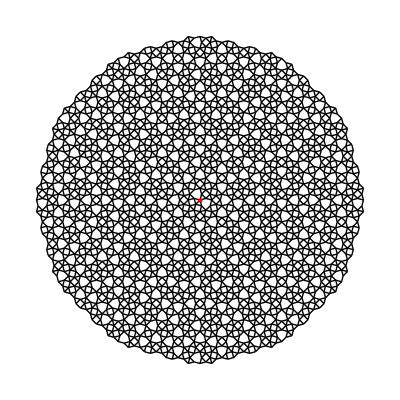

```mathematica
edgeplot0=Show[Graphics[Map[Line[{
Part[verts0,Part[#,1]+1],
Part[verts0,Part[#,2]+1]}]&,edgeIndices0]],
Graphics[{Red,Point[{0,0}]}]]
```

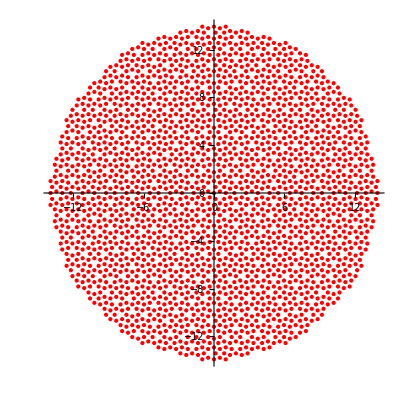

```mathematica
vertplot0=ListPlot[verts0,AspectRatio->1.0,PlotStyle->Red]
```

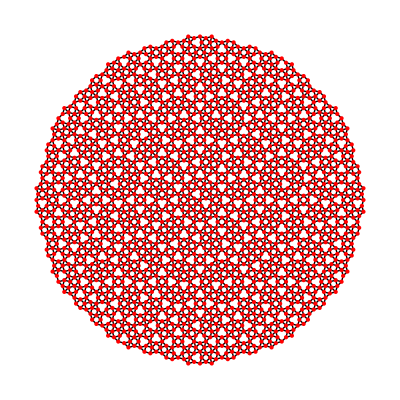

```mathematica
Show[edgeplot0,vertplot0]
```